# Find closest point on the MT

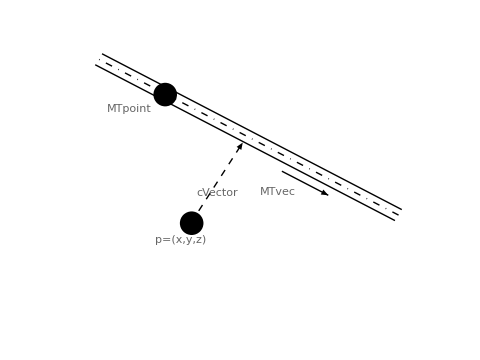

We have the situation shown above, where we want to find the vector cVector from the point (x,y,z) to closest point on the surface of the MT. The MT centerline is defined by a point MTpoint and a unit vector MTvec.

t=((MTpoint-p)·MTvec)MTvec
v=(MTpoint-p)-t
   =(MTpoint-p)- ((MTpoint-p)·MTvec)MTvec
cVector=v-R_MT v/(|v|)=(1-R_MT/(|v|))v

## Find the vector from the point to the closest point on the MT

```mathematica
pointToMTcenterVec=
({MTpoint[MTnum][0],MTpoint[MTnum][1],MTpoint[MTnum][2]}-{x,y,z})-Dot[{MTpoint[MTnum][0],MTpoint[MTnum][1],MTpoint[MTnum][2]}-{x,y,z},{MTvec[MTnum][0],MTvec[MTnum][1],MTvec[MTnum][2]}]*{MTvec[MTnum][0],MTvec[MTnum][1],MTvec[MTnum][2]}
```

{-x+MTpoint[MTnum][0]-MTvec[MTnum][0] ((-x+MTpoint[MTnum][0]) MTvec[MTnum][0]+(-y+MTpoint[MTnum][1]) MTvec[MTnum][1]+(-z+MTpoint[MTnum][2]) MTvec[MTnum][2]),-y+MTpoint[MTnum][1]-MTvec[MTnum][1] ((-x+MTpoint[MTnum][0]) MTvec[MTnum][0]+(-y+MTpoint[MTnum][1]) MTvec[MTnum][1]+(-z+MTpoint[MTnum][2]) MTvec[MTnum][2]),-z+MTpoint[MTnum][2]-MTvec[MTnum][2] ((-x+MTpoint[MTnum][0]) MTvec[MTnum][0]+(-y+MTpoint[MTnum][1]) MTvec[MTnum][1]+(-z+MTpoint[MTnum][2]) MTvec[MTnum][2])}

Alternate formulation from http://stackoverflow.com/questions/5227373/minimal-perpendicular-vector-between-a-point-and-a-line

```mathematica
altpointToMTcenterVec={MTpoint[MTnum][0],MTpoint[MTnum][1],MTpoint[MTnum][2]}+Dot[-{MTpoint[MTnum][0],MTpoint[MTnum][1],MTpoint[MTnum][2]}+{x,y,z},{MTvec[MTnum][0],MTvec[MTnum][1],MTvec[MTnum][2]}]*{MTvec[MTnum][0],MTvec[MTnum][1],MTvec[MTnum][2]} - {x,y,z}
```

{-x+MTpoint[MTnum][0]+MTvec[MTnum][0] ((x-MTpoint[MTnum][0]) MTvec[MTnum][0]+(y-MTpoint[MTnum][1]) MTvec[MTnum][1]+(z-MTpoint[MTnum][2]) MTvec[MTnum][2]),-y+MTpoint[MTnum][1]+MTvec[MTnum][1] ((x-MTpoint[MTnum][0]) MTvec[MTnum][0]+(y-MTpoint[MTnum][1]) MTvec[MTnum][1]+(z-MTpoint[MTnum][2]) MTvec[MTnum][2]),-z+MTpoint[MTnum][2]+MTvec[MTnum][2] ((x-MTpoint[MTnum][0]) MTvec[MTnum][0]+(y-MTpoint[MTnum][1]) MTvec[MTnum][1]+(z-MTpoint[MTnum][2]) MTvec[MTnum][2])}

They are the same

```mathematica
Thread[pointToMTcenterVec==altpointToMTcenterVec]//Simplify
```

{True,True,True}

```mathematica
pointToMTsurfaceVec=(1-RMT[MTnum]/Sqrt[Total[pointToMTcenterVec^2]])pointToMTcenterVec//Simplify
```

{(-x+MTpoint[MTnum][0]-MTvec[MTnum][0] ((-x+MTpoint[MTnum][0]) MTvec[MTnum][0]+(-y+MTpoint[MTnum][1]) MTvec[MTnum][1]+(-z+MTpoint[MTnum][2]) MTvec[MTnum][2])) (1-RMT[MTnum]/(√((x-MTpoint[MTnum][0]+MTvec[MTnum][0] ((-x+MTpoint[MTnum][0]) MTvec[MTnum][0]+(-y+MTpoint[MTnum][1]) MTvec[MTnum][1]+(-z+MTpoint[MTnum][2]) MTvec[MTnum][2]))^2+(y-MTpoint[MTnum][1]+MTvec[MTnum][1] ((-x+MTpoint[MTnum][0]) MTvec[MTnum][0]+(-y+MTpoint[MTnum][1]) MTvec[MTnum][1]+(-z+MTpoint[MTnum][2]) MTvec[MTnum][2]))^2+(z-MTpoint[MTnum][2]+MTvec[MTnum][2] ((-x+MTpoint[MTnum][0]) MTvec[MTnum][0]+(-y+MTpoint[MTnum][1]) MTvec[MTnum][1]+(-z+MTpoint[MTnum][2]) MTvec[MTnum][2]))^2))),(-y+MTpoint[MTnum][1]-MTvec[MTnum][1] ((-x+MTpoint[MTnum][0]) MTvec[MTnum][0]+(-y+MTpoint[MTnum][1]) MTvec[MTnum][1]+(-z+MTpoint[MTnum][2]) MTvec[MTnum][2])) (1-RMT[MTnum]/(√((x-MTpoint[MTnum][0]+MTvec[MTnum][0] ((-x+MTpoint[MTnum][0]) MTvec[MTnum][0]+(-y+MTpoint[MTnum][1]) MTvec[MTnum][1]+(-z+MTpoint[MTnum][2]) MTvec[MTnum][2]))^2+(y-MTpoint[MTnum][1]+MTvec[MTnum][1] ((-x+MTpoint[MTnum][0]) MTvec[MTnum][0]+(-y+MTpoint[MTnum][1]) MTvec[MTnum][1]+(-z+MTpoint[MTnum][2]) MTvec[MTnum][2]))^2+(z-MTpoint[MTnum][2]+MTvec[MTnum][2] ((-x+MTpoint[MTnum][0]) MTvec[MTnum][0]+(-y+MTpoint[MTnum][1]) MTvec[MTnum][1]+(-z+MTpoint[MTnum][2]) MTvec[MTnum][2]))^2))),(-z+MTpoint[MTnum][2]-MTvec[MTnum][2] ((-x+MTpoint[MTnum][0]) MTvec[MTnum][0]+(-y+MTpoint[MTnum][1]) MTvec[MTnum][1]+(-z+MTpoint[MTnum][2]) MTvec[MTnum][2])) (1-RMT[MTnum]/(√((x-MTpoint[MTnum][0]+MTvec[MTnum][0] ((-x+MTpoint[MTnum][0]) MTvec[MTnum][0]+(-y+MTpoint[MTnum][1]) MTvec[MTnum][1]+(-z+MTpoint[MTnum][2]) MTvec[MTnum][2]))^2+(y-MTpoint[MTnum][1]+MTvec[MTnum][1] ((-x+MTpoint[MTnum][0]) MTvec[MTnum][0]+(-y+MTpoint[MTnum][1]) MTvec[MTnum][1]+(-z+MTpoint[MTnum][2]) MTvec[MTnum][2]))^2+(z-MTpoint[MTnum][2]+MTvec[MTnum][2] ((-x+MTpoint[MTnum][0]) MTvec[MTnum][0]+(-y+MTpoint[MTnum][1]) MTvec[MTnum][1]+(-z+MTpoint[MTnum][2]) MTvec[MTnum][2]))^2)))}

## The associated distance

```mathematica
dist=Sqrt[Total[{cVector[0],cVector[1],cVector[2]}^2]]
```

√(cVector[0]^2+cVector[1]^2+cVector[2]^2)

## The associated point

```mathematica
closestPoint={x,y,z}+{cVector[0],cVector[1],cVector[2]}
```

{x+cVector[0],y+cVector[1],z+cVector[2]}

## Write to file

```mathematica
DeleteFile[NotebookDirectory[]<>"pointToMT_formulae.txt"]
outfileLoc=CreateFile[NotebookDirectory[]<>"pointToMT_formulae.txt"];
outfile=File[outfileLoc];
```

```mathematica
WriteString[outfile,CForm[cVector[0]==pointToMTsurfaceVec[[1]]],";","\n"]
WriteString[outfile,CForm[cVector[1]==pointToMTsurfaceVec[[2]]],";","\n"]
WriteString[outfile,CForm[cVector[2]==pointToMTsurfaceVec[[3]]],";","\n\n"]

WriteString[outfile,CForm[MTdist ==dist],";","\n\n"];

WriteString[outfile,CForm[cPoint[0]==closestPoint[[1]]],";","\n"]
WriteString[outfile,CForm[cPoint[1]==closestPoint[[2]]],";","\n"]
WriteString[outfile,CForm[cPoint[2]==closestPoint[[3]]],";","\n"]
```

```mathematica
Close[outfile]
```

/Users/Matt/project_code/Motor_Freedom/tools/pointToMT_formulae.txt

## Testing

```mathematica
testvecs={RMT[MTnum]->.2,
MTpoint[MTnum][0]->.2356,MTpoint[MTnum][1]->-1,MTpoint[MTnum][2]->.0,
x->0,y->0,z->0,
MTvec[MTnum][0]->Sqrt[2]/2,MTvec[MTnum][1]->Sqrt[2]/2,MTvec[MTnum][2]->0}
```

{RMT[MTnum]→0.2,MTpoint[MTnum][0]→0.2356,MTpoint[MTnum][1]→-1,MTpoint[MTnum][2]→0.,x→0,y→0,z→0,MTvec[MTnum][0]→1/(√2),MTvec[MTnum][1]→1/(√2),MTvec[MTnum][2]→0}

```mathematica
pointToMTsurfaceVec/.testvecs
```

{0.476379,-0.476379,0.}

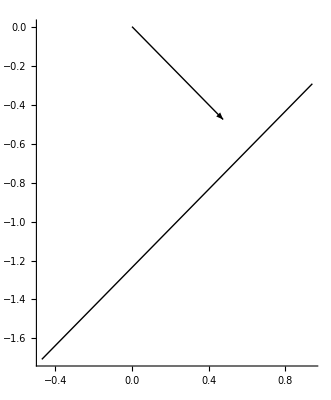

```mathematica
Graphics[{Arrow[{{x,y},{x+pointToMTsurfaceVec[[1]],y+pointToMTsurfaceVec[[2]]}}],
Line[{{MTpoint[MTnum][0],MTpoint[MTnum][1]}+{MTvec[MTnum][0],MTvec[MTnum][1]},{MTpoint[MTnum][0],MTpoint[MTnum][1]}-{MTvec[MTnum][0],MTvec[MTnum][1]}}]}/.testvecs,Axes->True]
```

```mathematica
testvecs3D={RMT[MTnum]->.1,
MTpoint[MTnum][0]->1,MTpoint[MTnum][1]->1,MTpoint[MTnum][2]->1,
x->0,y->-1,z->0,
MTvec[MTnum][0]->1/Sqrt[3],MTvec[MTnum][1]->1/Sqrt[3],MTvec[MTnum][2]->1/Sqrt[3]}
```

{RMT[MTnum]→0.1,MTpoint[MTnum][0]→1,MTpoint[MTnum][1]→1,MTpoint[MTnum][2]→1,x→0,y→-1,z→0,MTvec[MTnum][0]→1/(√3),MTvec[MTnum][1]→1/(√3),MTvec[MTnum][2]→1/(√3)}

```mathematica
Graphics3D[{Arrow[{{x,y,z},{x+pointToMTsurfaceVec[[1]],y+pointToMTsurfaceVec[[2]],z+pointToMTsurfaceVec[[3]]}}],
Line[{{MTpoint[MTnum][0],MTpoint[MTnum][1],MTpoint[MTnum][2]}+{MTvec[MTnum][0],MTvec[MTnum][1],MTvec[MTnum][2]},{MTpoint[MTnum][0],MTpoint[MTnum][1],MTpoint[MTnum][2]}-3{MTvec[MTnum][0],MTvec[MTnum][1],MTvec[MTnum][2]}}]}/.testvecs3D,Axes->True]
```

-Graphics3D-

```mathematica
simvecs={RMT[MTnum]->.012,
MTpoint[MTnum][0]->0,MTpoint[MTnum][1]->0,MTpoint[MTnum][2]->-.312,
x->0,y->0,z->-.25,
MTvec[MTnum][0]->1,MTvec[MTnum][1]->0,MTvec[MTnum][2]->0}
```

{RMT[MTnum]→0.012,MTpoint[MTnum][0]→0,MTpoint[MTnum][1]→0,MTpoint[MTnum][2]→-0.312,x→0,y→0,z→-0.25,MTvec[MTnum][0]→1,MTvec[MTnum][1]→0,MTvec[MTnum][2]→0}

```mathematica
pointToMTsurfaceVec/.simvecs
```

{0.,0.,-0.05}